```mathematica
Quit[]
```

## USR2SR

```mathematica
$Assumptions={ϵ0>0,τ<0,τ0<0,H>0,k>0,p>0,xe>0};
```

```mathematica
ζk[τ_,k_]=H/Sqrt[4ϵ0 k^3](τ0/τ)^3(1+I k τ)E^(-I k τ);
```

```mathematica
ζkp[τ_,k_]=D[ζk[τ,k], τ]//Simplify
```

(ⅇ^(-ⅈ k τ) H (-3-3 ⅈ k τ+k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
Normal[Series[ζkp[τ,k],{τ,0,1}]]
```

-(H k^(5/2) τ0^3)/(16 √ϵ0)-(3 H τ0^3)/(2 k^(3/2) √ϵ0 τ^4)-(H √k τ0^3)/(4 √ϵ0 τ^2)+(ⅈ H k^(7/2) τ τ0^3)/(30 √ϵ0)

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

(ⅇ^(ⅈ k τ) H (1-ⅈ k τ) τ0^3)/(2 √(k^3 ϵ0) τ^3)

```mathematica
ζksp[τ_,k_]=D[ζks[τ,k], τ]//Simplify
```

(ⅇ^(ⅈ k τ) H (-3+3 ⅈ k τ+k^2 τ^2) τ0^3)/(2 √(k^3 ϵ0) τ^4)

```mathematica
Normal[Series[ζk[τ,k]ζksp[τ,k],{τ,0,0}]]
```

-(3 H^2 τ0^6)/(4 k^3 ϵ0 τ^7)-(H^2 τ0^6)/(2 k ϵ0 τ^5)+(ⅈ H^2 τ0^6)/(4 ϵ0 τ^4)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

(H^2 (1+k^2 τ^2) τ0^6)/(4 k^3 ϵ0 τ^6)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τ0,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

H^2/(4 k^3 x^6 ϵ0)

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp) (ⅈ+p τp) (-3+3 ⅈ k τp+k^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
pktk[xe τ0,xe τ0,p,k]//Simplify
```

(H^6 (-ⅈ+k xe τ0)^2 (ⅈ+k xe τ0) (1+ⅈ p xe τ0) (ⅈ+p xe τ0) (-3+3 ⅈ k xe τ0+k^2 xe^2 τ0^2))/(64 k^6 p^3 xe^19 ϵ0^3 τ0)

```mathematica
5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe Im[pktk[xe τ0,xe τ0,p,k]//Expand]2)/(PUSR[xe,p]PUSR[xe,k])//Simplify
```

5/12 Δηe (1+k^2 xe^2 τ0^2) (1+p^2 xe^2 τ0^2)

```mathematica
pktkim[xe_,p_,k_]=Normal[Series[pktk[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^3 p^3 xe^16 ϵ0^3)

```mathematica
Normal[Series[5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe pktkim[xe,p,k]2)/(PUSR[xe,p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,k]ζk[τ,k]ζk[τ,p]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

(ⅇ^(-ⅈ (2 k+p) (τ-τp)) H^6 (-ⅈ+k τ)^2 (1+ⅈ p τ) τ0^18 (ⅈ+k τp)^2 (-3+3 ⅈ p τp+p^2 τp^2))/(64 k^6 p^3 ϵ0^3 τ^9 τp^10)

```mathematica
kktpim[xe_,p_,k_]=Normal[Series[kktp[xe τ0,xe τ0,p,k],{xe,0,-16}]]//ExpToTrig//Simplify//Im//Simplify
```

(H^6 τ0^2)/(64 k^6 xe^16 ϵ0^3)

```mathematica
Normal[Series[5/12(2/(xe^2 τ0^2 H^2)xe^6 ϵ0 Δηe kktpim[xe,p,k]2)/(PUSR[xe,p]PUSR[xe,k]),{xe,0,0}]]
```

(5 p^3 Δηe)/(12 k^3)

## SR2USR2SR sharp

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//Simplify
```

1/(16 k^9 ϵSR τ^6)H^2 (3 ⅇ^(ⅈ k (τ-2 τs)) (ⅈ+k τ) (-ⅈ+k τs)^2+ⅇ^(-ⅈ k τ) (1+ⅈ k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs)))

```mathematica
PSR[p_]=Normal[Series[Pk[τ,p],{p,0,-3}]]
```

H^2/(4 p^3 ϵSR)

```mathematica
PUSR[x_,k_]=Normal[Series[Pk[x τs,k],{x,0,-6}]]//ExpToTrig//FullSimplify
```

(H^2 (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6+3 (-3+7 k^4 τs^4) Cos[2 k τs]+6 k τs (-3-4 k^2 τs^2+k^4 τs^4) Sin[2 k τs]))/(8 k^9 x^6 ϵSR τs^6)

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

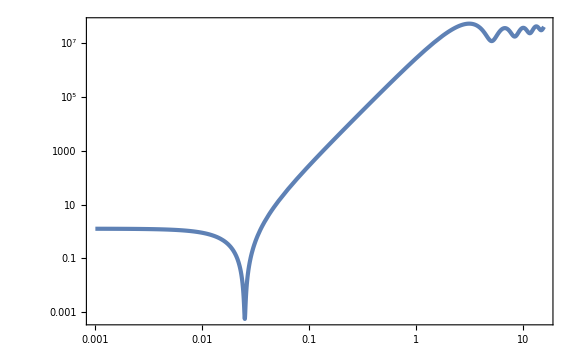

```mathematica
LogLogPlot[calPk[-10^-1.2,k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^1.2}]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

```mathematica
nsm1e[k_]=Normal[Series[nsm1[xe τs,k],{xe,0,0}]]//Simplify
```

(6 (9+18 ⅈ k τs-6 k^2 τs^2+12 ⅈ k^3 τs^3-15 k^4 τs^4-8 ⅈ k^5 τs^5+2 k^6 τs^6-6 ⅇ^(2 ⅈ k τs) (3+4 k^2 τs^2+k^4 τs^4)+ⅇ^(4 ⅈ k τs) (9-18 ⅈ k τs-6 k^2 τs^2-12 ⅈ k^3 τs^3-15 k^4 τs^4+8 ⅈ k^5 τs^5+2 k^6 τs^6)))/((3+3 k^2 τs^2+2 ⅈ k^3 τs^3+3 ⅇ^(2 ⅈ k τs) (ⅈ+k τs)^2) (3 (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (3+3 k^2 τs^2-2 ⅈ k^3 τs^3)))

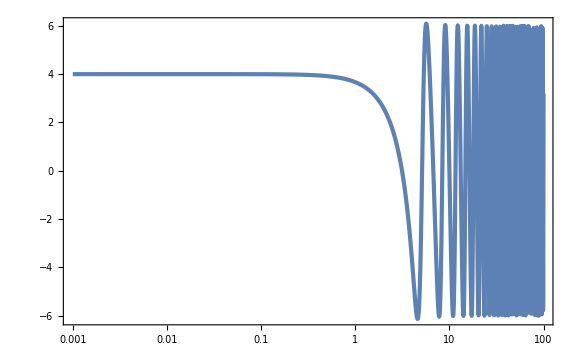

```mathematica
LogLinearPlot[nsm1e[k]/.{τs->-1},{k,10^-3,10^2},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
pktkeim[xe_,p_,k_]=Normal[Series[pktk[xe τs,xe τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

1/(128 k^9 p^3 xe^10 ϵSR^3 τs^4)H^6 ((1+k^2 xe^2 τs^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)+(-9-9 k^2 xe^2 τs^2+3 k^4 (7+4 xe^3) τs^4+k^6 xe^2 (21+16 xe) τs^6-4 k^8 xe^3 τs^8) Cos[2 k τs]+2 k τs (-9-3 k^2 (4+3 xe^2+xe^3) τs^2+3 k^4 (1-4 xe^2) τs^4+k^6 xe^2 (3+7 xe) τs^6) Sin[2 k τs])

```mathematica
Normal[Series[5/12(2/(xe^2 τs^2 H^2)xe^6 ϵSR Δηe pktkeim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]
```

(5 Δηe)/12

```mathematica
pktksim[xe_,p_,k_]=Normal[Series[pktk[xe τs,τs,p,k],{p,0,-3},{xe,0,-6}]]//ExpToTrig//Expand//Im//FullSimplify
```

1/(128 k^9 p^3 xe^6 ϵSR^3 τs^4)H^6 (3 (3+4 k^2 τs^2+k^4 τs^4)+(-9+6 k^2 τs^2+15 k^4 τs^4-2 k^6 τs^6) Cos[2 k τs]+2 k τs (-9-6 k^2 τs^2+4 k^4 τs^4) Sin[2 k τs])

```mathematica
fNLpktks[x_]=Normal[Series[5/12(2/(τs^2 H^2)ϵSR Δηe pktksim[xe,p,k]2)/(PSR[p]PUSR[xe,k]),{xe,0,0}]]/.{k->x/τs}//Simplify
```

(5 Δηe (3 (3+4 x^2+x^4)+(-9+6 x^2+15 x^4-2 x^6) Cos[2 x]+2 x (-9-6 x^2+4 x^4) Sin[2 x]))/(12 (9+18 x^2+9 x^4+2 x^6+3 (-3+7 x^4) Cos[2 x]+6 x (-3-4 x^2+x^4) Sin[2 x]))

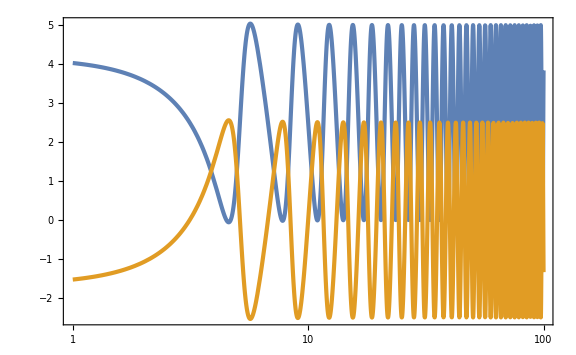

```mathematica
LogLinearPlot[{fNLpktks[x]+5/2/.{Δηe->-6},-5/12 nsm1e[x]/.{τs->-1}},{x,10^0,10^2},WorkingPrecision->30]
```

```mathematica
kktp[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,k]ζks[τp,k]D[ζks[τp,p], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (3 (-3-3 ⅈ p τp+p^2 τp^2) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (-3+3 ⅈ p τp+p^2 τp^2) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
kktpeim[xe_,p_,k_]=Normal[Series[kktp[xe τs,xe τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

```mathematica
kktpsim[xe_,p_,k_]=Normal[Series[kktp[xe τs,τs,p,k],{p,0,-3},{x,0,-6}]]//ExpToTrig//Simplify//Im//Simplify
```

0

## SR2USR2SR sharp specific value

```mathematica
$Assumptions={ϵSR>0,τ<0,τs<0,H>0,k>0,p>0,xe>0};
```

```mathematica
Ak[k_]=1-(3(1+k^2 τs^2))/(2I k^3 τs^3);
Bk[k_]=-(3(1+I k τs)^2)/(2I k^3 τs^3)Exp[-2I k τs];
ζk[τ_,k_]=(I H)/(2Sqrt[ϵSR])(τs/τ)^3 1/k^(3/2)(Ak[k] E^(-I k τ)(1+I k τ)-Bk[k] E^(I k τ)(1-I k τ));
```

```mathematica
ζks[τ_,k_]=Conjugate[ζk[τ,k]]//FullSimplify
```

-(ⅈ H (3 ⅇ^(-ⅈ k (τ-2 τs)) (-ⅈ+k τ) (ⅈ+k τs)^2+ⅇ^(ⅈ k τ) (1-ⅈ k τ) (-3 ⅈ+k^2 τs^2 (-3 ⅈ+2 k τs))))/(4 √(k^9 ϵSR) τ^3)

```mathematica
Pk[τ_,k_]=ζks[τ,k]ζk[τ,k]//ExpToTrig//Expand//Simplify
```

1/(8 k^9 ϵSR τ^6)H^2 ((1+k^2 τ^2) (9+18 k^2 τs^2+9 k^4 τs^4+2 k^6 τs^6)-3 (3-3 k^2 τ (τ-4 τs)+k^4 (16 τ-7 τs) τs^3+k^6 τ (7 τ-4 τs) τs^4) Cos[2 k (τ-τs)]+6 k (3 τs+4 k^2 τs^3-k^4 τs^5+k^2 τ^2 τs (-3-4 k^2 τs^2+k^4 τs^4)+τ (-3+7 k^4 τs^4)) Sin[2 k (τ-τs)])

```mathematica
calPk[τ_,k_]=k^3/(2 π^2)Pk[τ,k];
```

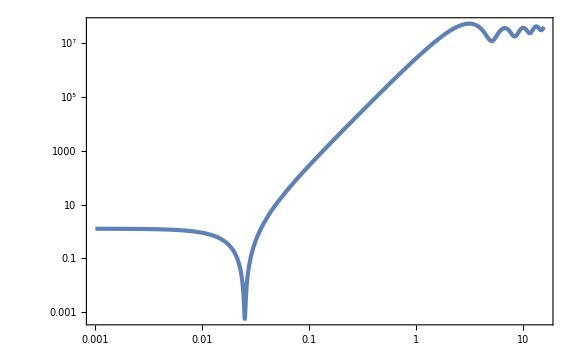

```mathematica
LogLogPlot[calPk[-10^(-12/10),k]/.{ϵSR->10^-2,H->1,τs->-1},{k,10^-3,10^(12/10)},WorkingPrecision->30]
```

```mathematica
nsm1[τ_,k_]=k D[Log[calPk[τ,k]], k]//Simplify;
```

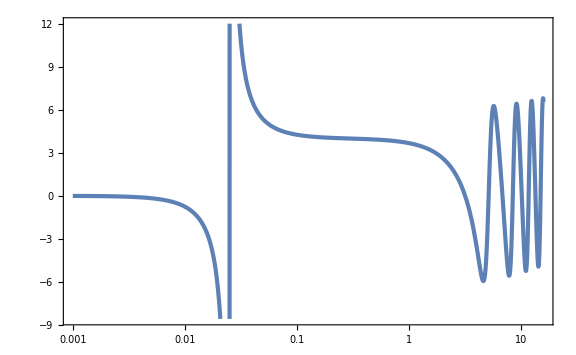

```mathematica
LogLinearPlot[nsm1[-10^(-12/10),k]/.{τs->-1},{k,10^-3,10^(12/10)},WorkingPrecision->30]
```

```mathematica
pktk[τ_,τp_,p_,k_]=ζk[τ,p]ζk[τ,k]ζk[τ,k]ζks[τp,p]ζks[τp,k]D[ζks[τp,k], τp]//Simplify
```

1/(4096 k^18 p^9 ϵSR^3 τ^9 τp^10)ⅇ^(-ⅈ (2 k+p) (τ+τp)) H^6 (3 (1+ⅈ k τp) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (ⅈ+k τp) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (-3 ⅈ (-3-3 ⅈ k τp+k^2 τp^2) (ⅈ+k τs)^2+ⅇ^(2 ⅈ k (τp-τs)) (-3+3 ⅈ k τp+k^2 τp^2) (-3 ⅈ-3 ⅈ k^2 τs^2+2 k^3 τs^3)) (3 ⅇ^(2 ⅈ k τ) (1-ⅈ k τ) (-ⅈ+k τs)^2+ⅇ^(2 ⅈ k τs) (-ⅈ+k τ) (3 ⅈ+3 ⅈ k^2 τs^2+2 k^3 τs^3))^2 (-3 (-ⅈ+p τp) (ⅈ+p τs)^2+ⅇ^(2 ⅈ p (τp-τs)) (ⅈ+p τp) (3+3 p^2 τs^2+2 ⅈ p^3 τs^3)) (3 ⅇ^(2 ⅈ p τ) (1-ⅈ p τ) (-ⅈ+p τs)^2+ⅇ^(2 ⅈ p τs) (-ⅈ+p τ) (3 ⅈ+3 ⅈ p^2 τs^2+2 p^3 τs^3))

```mathematica
fNLe[p_,k_]=5/3 1/(xe^2 τs^2 H^2)(xe^6 ϵSR Δηe Im[pktk[xe τs,xe τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

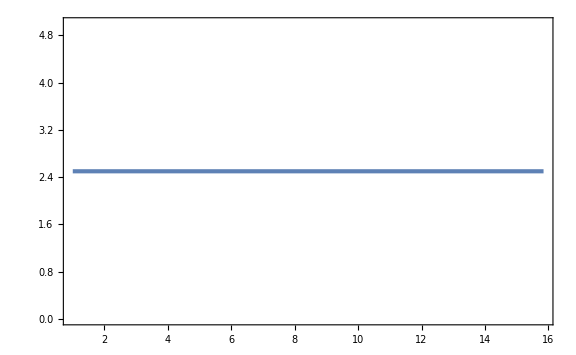

```mathematica
Plot[fNLe[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},{k,1,10^(12/10)},WorkingPrecision->30]
```

```mathematica
fNLs[p_,k_]=-5/3 1/(τs^2 H^2)(ϵSR Δηe Im[pktk[xe τs,τs,p,k]])/(Pk[xe τs,p]Pk[xe τs,k]);
```

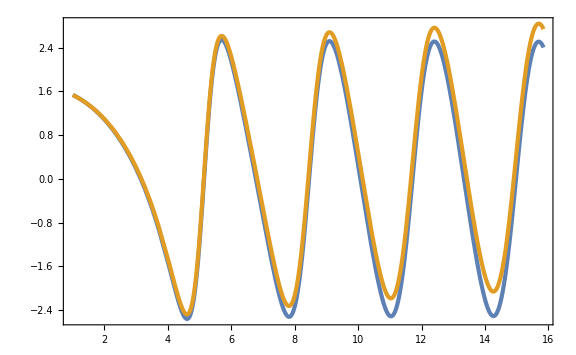

```mathematica
Plot[{fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

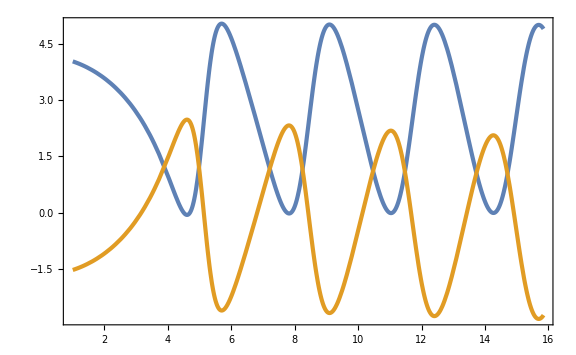

```mathematica
Plot[{fNLe[10^-3,k]+fNLs[10^-3,k]/.{xe->10^(-12/10),τs->-1,H->1,ϵSR->10^-2,Δηe->6},-5/12 nsm1[-10^(-12/10),k]/.{τs->-1}},{k,1,10^(12/10)},WorkingPrecision->30]
```

## SR2USR

```mathematica
$Assumptions={ϵ0>0,τ0<0,τs<0,τ<0};
```

```mathematica
η[τ_]=-6 (1-Tanh[Log[τ/τs]/(5 10^-2)])/2//Simplify
```

3 (-1+Tanh[20 Log[τ/τs]])

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
Log10[(10^-2/(2 10^-9))^(1/4)]//N
```

1.67474

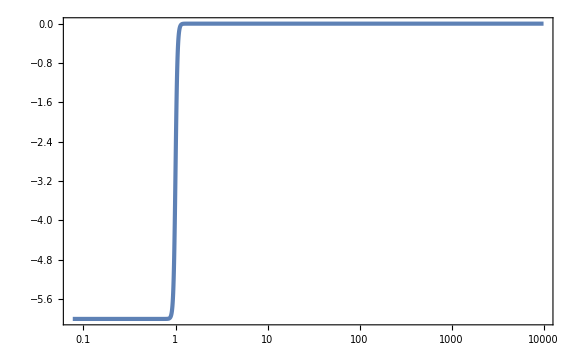

```mathematica
LogLinearPlot[η[-x]/.{τs->-1},{x,10^-lndt,10^4}]
```

```mathematica
ηint[τ_]=Integrate[-η[τ]/τ,τ]//Simplify
```

6 Log[τ]-3/20 Log[τ^40+τs^40]

```mathematica
ϵ[τ_]=ϵ0 Exp[ηint[τ]-ηint[τ0]]//Simplify
```

(ϵ0 τ^6 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/20))/τ0^6

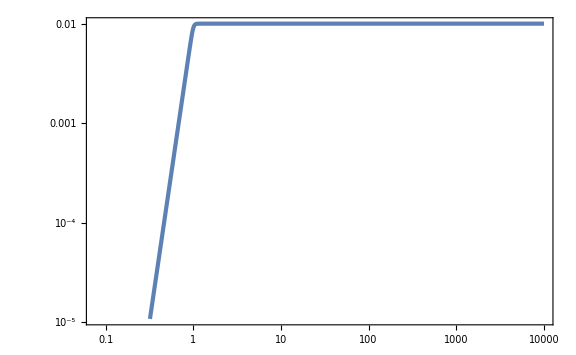

```mathematica
LogLogPlot[ϵ[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
z[τ_]=-1/(τ H)Sqrt[2ϵ[τ]]/.{H->1}//Simplify
```

-(√2 √ϵ0 τ^2 ((τ0^40+τs^40)/(τ^40+τs^40))^(3/40))/τ0^3

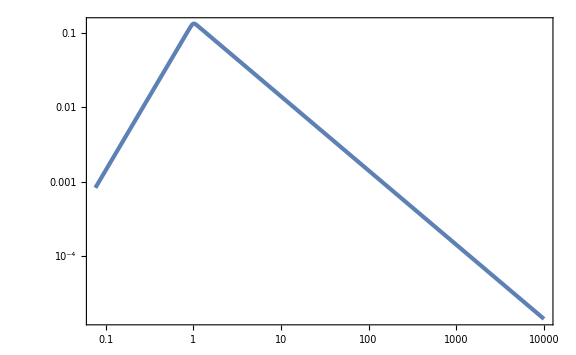

```mathematica
LogLogPlot[z[-x]/.{τs->-1,τ0->-10^4,ϵ0->10^-2},{x,10^-lndt,10^4}]
```

```mathematica
EoM=vk''[τ]+(k^2-z''[τ]/z[τ])vk[τ]==0//Simplify
```

((-2 τ^80+k^2 τ^82+125 τ^40 τs^40+2 k^2 τ^42 τs^40-2 τs^80+k^2 τ^2 τs^80) vk[τ])/(τ^2 (τ^40+τs^40)^2)+vk''[τ]==0

```mathematica
kL=3 10^-3;
kS=8.5;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10^4,k->kL},vk[τ],{τ,-10^4,-10^-lndt}(*,WorkingPrecision->30,MaxSteps->10^6*)][[1]];//AbsoluteTiming
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->-10,k->kS},vk[τ],{τ,-10,-10^-lndt}(*,WorkingPrecision->20,MaxSteps->10^5*)][[1]];//AbsoluteTiming
```

{0.006995,Null}

{0.003034,Null}

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^4,ϵ0->10^-2};
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
PζkS[τ_]=Norm[ζkS[τ]]^2;
```

```mathematica
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
```

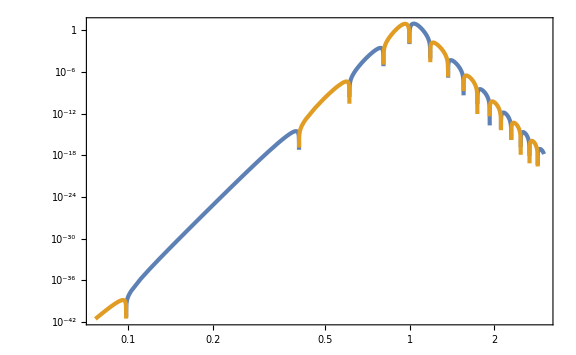

```mathematica
LogLogPlot[{5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]],-5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2Im[2/τp^2(ϵ[-τp]η'[-τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,-τp]]},{τp,10^-lndt,3}]
```

```mathematica
5/12 1/(PζkL[-10^-lndt]PζkS[-10^-lndt])2NIntegrate[Im[2/τp^2(ϵ[τp]η'[τp]/.{τs->-1,τ0->-10^4,ϵ0->10^-2})pktk[-10^-lndt,τp]],{τp,-10,-10^-lndt}]
```

0.0775123

## SR2USR2SR num

```mathematica
$Assumptions={ϵ0>0,τ0<0,τi<0,τs<0,τ<0,lnDt>0};
```

```mathematica
lndt=Log10[(10^-2/(2 10^-9))^(1/6)];lndt//N
```

1.1165

```mathematica
dN=5 10^-2;
ηs[τ_]=-6 (1-Tanh[Log[τ/τs]/dN])/2/.{τs->-1}//FullSimplify
ηe[τ_]=-6(1-Tanh[Log[(τs 10^-lnDt)/τ]/dN])/2/.{τs->-1,lnDt->lndt}//FullSimplify
ηsp[τ_]=ηs'[τ]//Simplify
ηep[τ_]=ηe'[τ]//Simplify
```

-6/(1+τ^40)

3 (-1+Tanh[20 Log[-1/(10 5^(1/6) τ)]])

(240 τ^39)/((1+τ^40)^2)

-(60 Sech[20 Log[-1/(10 5^(1/6) τ)]]^2)/τ

```mathematica
τsm=τ/.Solve[Log[τ/τs]/dN==10/.{τs->-1},τ][[1]];
τsp=τ/.Solve[Log[τ/τs]/dN==-10/.{τs->-1},τ][[1]];
τem=τ/.Solve[Log[(τs 10^-lnDt)/τ]/dN==-10/.{τs->-1,lnDt->lndt},τ][[1]];
τep=τ/.Solve[Log[(τs 10^-lnDt)/τ]/dN==10/.{τs->-1,lnDt->lndt},τ][[1]];
τsm//N
τsp//N
τem//N
τep//N
```

-1.64872

-0.606531

-0.126082

-0.0463829

```mathematica
Clear[η,ηp]
η[τ_]:=ηs[τ]/;(τsm<τ<τsp)
η[τ_]:=ηe[τ]/;(τem<τ<τep)
η[τ_]:=-6/;(τsp<=τ<=τem)
η[τ_]:=0/;(τ<=τsm||τ>=τep)
ηp[τ_]:=ηsp[τ]/;(τsm<τ<τsp)
ηp[τ_]:=ηep[τ]/;(τem<τ<τep)
ηp[τ_]:=0/;!((τsm<τ<τsp)||(τem<τ<τep))
```

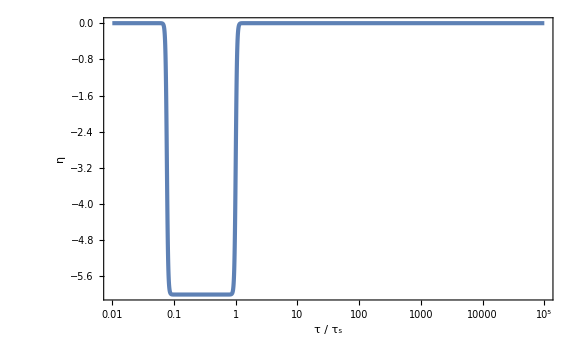

```mathematica
LogLinearPlot[η[-x],{x,10^-2,10^5},PlotRange->Full,FrameLabel->{"τ / τ_s",η}]
```

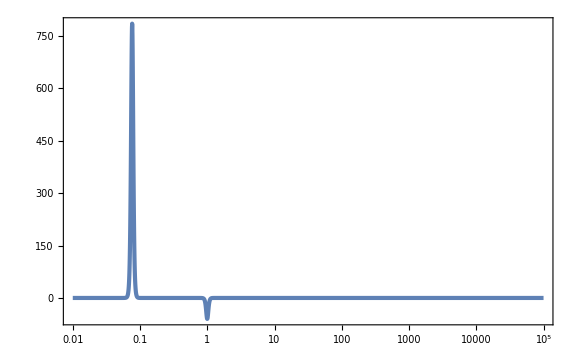

```mathematica
LogLinearPlot[ηp[-x],{x,10^-2,10^5},PlotRange->Full]
```

```mathematica
ηsint[τ_]=Integrate[-ηs[τ]/τ,τ]//Simplify
ηeint[τ_]=Integrate[-ηe[τ]/τ,τ]//Simplify
ηUSRint[τ_]=Integrate[6/τ,τ]//Simplify
```

6 (Log[τ]-1/40 Log[1+τ^40])

3 Log[τ]+3/20 Log[Cosh[20 Log[-1/(10 5^(1/6) τ)]]]

6 Log[τ]

```mathematica
ηint1[τ_]=ηsint[τ]-ηsint[τsm]//Simplify
ηint2[τ_]=ηUSRint[τ]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify
ηint3[τ_]=ηeint[τ]-ηeint[τem]+ηUSRint[τem]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify//Re
ηint4=ηeint[τep]-ηeint[τem]+ηUSRint[τem]-ηUSRint[τsp]+ηsint[τsp]-ηsint[τsm]//Simplify
```

3/20 (-20+Log[1+ⅇ^20]+40 Log[-τ]-Log[1+τ^40])

6 Log[-τ]

-3/2-Log[5000000]/2+Re[3 Log[τ]+3/20 Log[ⅇ^20 Cosh[20 Log[-1/(10 5^(1/6) τ)]] Sech[10]]]

-Log[5000000]

```mathematica
Clear[ηint]
ηint[τ_]:=0/;τ<=τsm
ηint[τ_]:=ηint1[τ]/;τsm<τ<τsp
ηint[τ_]:=ηint2[τ]/;τsp<=τ<=τem
ηint[τ_]:=ηint3[τ]/;τem<τ<τep
ηint[τ_]:=ηint4/;τep<=τ
```

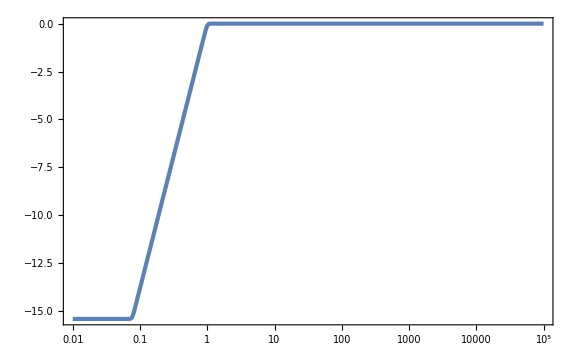

```mathematica
LogLinearPlot[ηint[-x],{x,10^-2,10^5}]
```

```mathematica
ϵ1[τ_]=ϵ0 Exp[ηint1[τ]]/.{ϵ0->10^-2}//Simplify
ϵ2[τ_]=ϵ0 Exp[ηint2[τ]]/.{ϵ0->10^-2}//Simplify
ϵ3[τ_]=ϵ0 Exp[ηint3[τ]]/.{ϵ0->10^-2}//Simplify
ϵ4=ϵ0 Exp[ηint4]/.{ϵ0->10^-2}//Simplify
```

((1+ⅇ^20)^(3/20) τ^6)/(100 ⅇ^3 (1+τ^40)^(3/20))

τ^6/100

-(ⅇ^(3/2) τ^3 Cosh[20 Log[-1/(10 5^(1/6) τ)]]^(3/20) Sech[10]^(3/20))/(100000 √5)

1/500000000

```mathematica
Clear[ϵ]
ϵ[τ_]:=(ϵ0/.{ϵ0->10^-2})/;τ<=τsm
ϵ[τ_]:=ϵ1[τ]/;τsm<τ<τsp
ϵ[τ_]:=ϵ2[τ]/;τsp<=τ<=τem
ϵ[τ_]:=ϵ3[τ]/;τem<τ<τep
ϵ[τ_]:=ϵ4/;τep<=τ
```

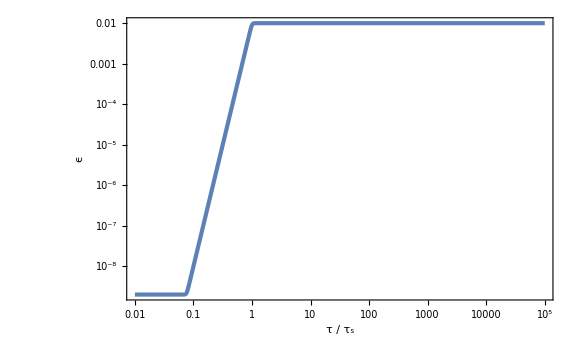

```mathematica
LogLogPlot[ϵ[-x],{x,10^-2,10^5},WorkingPrecision->30,FrameLabel->{"τ / τ_s",ϵ}]
```

```mathematica
Hs=H/.Solve[1/(2 10^-2)(H/(2π))^2==2 10^-9,H][[2]]
z0[τ_]=-1/(τ H)Sqrt[2ϵ0]/.{ϵ0->10^-2,H->Hs}//Simplify;
z1[τ_]=-1/(τ H)Sqrt[2ϵ1[τ]]/.{H->Hs}//Simplify;
z2[τ_]=-1/(τ H)Sqrt[2ϵ2[τ]]/.{H->Hs}//Simplify;
z3[τ_]=-1/(τ H)Sqrt[2ϵ3[τ]]/.{H->Hs}//Simplify;
z4[τ_]=-1/(τ H)Sqrt[2ϵ4]/.{H->Hs}//Simplify;
```

π/(25000 √10)

```mathematica
Clear[z]
z[τ_]:=z0[τ]/;τ<=τsm
z[τ_]:=z1[τ]/;τsm<τ<τsp
z[τ_]:=z2[τ]/;τsp<=τ<=τem
z[τ_]:=z3[τ]/;τem<τ<τep
z[τ_]:=z4[τ]/;τep<=τ
```

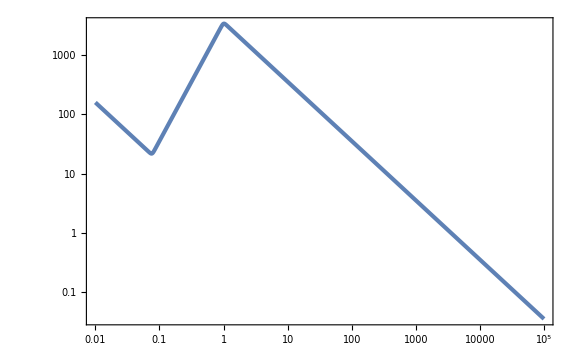

```mathematica
LogLogPlot[z[-x],{x,10^-2,10^5},WorkingPrecision->30]
```

```mathematica
zpp0[τ_]=z0''[τ]//Simplify;
zpp1[τ_]=z1''[τ]//Simplify;
zpp2[τ_]=z2''[τ]//Simplify;
zpp3[τ_]=z3''[τ];
zpp4[τ_]=z4''[τ]//Simplify;
```

```mathematica
Clear[zpp]
zpp[τ_]:=zpp0[τ]/;τ<=τsm
zpp[τ_]:=zpp1[τ]/;τsm<τ<τsp
zpp[τ_]:=zpp2[τ]/;τsp<=τ<=τem
zpp[τ_]:=zpp3[τ]/;τem<τ<τep
zpp[τ_]:=zpp4[τ]/;τep<=τ
```

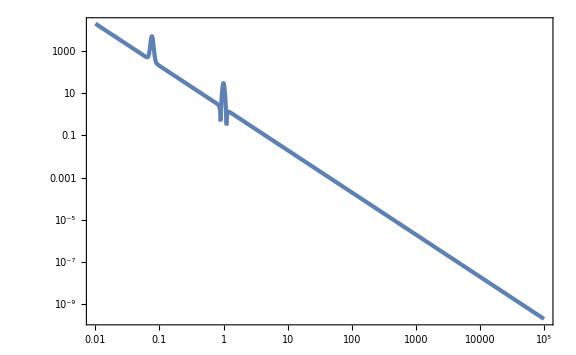

```mathematica
LogLogPlot[Abs[zpp[-x]/z[-x]],{x,10^-2,10^5},WorkingPrecision->30]
```

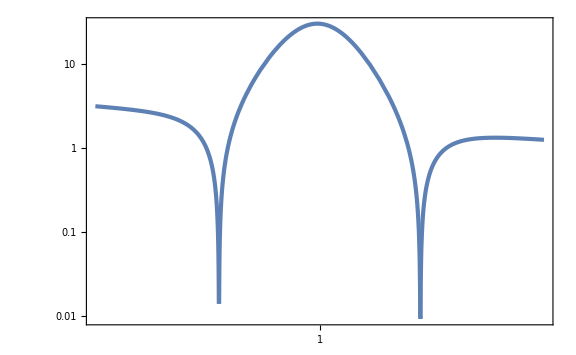

```mathematica
LogLogPlot[Abs[zpp[-x]/z[-x]],{x,10^-0.1,10^0.1},WorkingPrecision->30,PlotRange->Full]
```

```mathematica
EoM=vk''[τ]+(k^2-zpp[τ]/z[τ])vk[τ]==0//Simplify
```

vk[τ] (k^2-zpp[τ]/z[τ])+vk''[τ]==0

### kL = 1e-3

```mathematica
kL=10^-3;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==1/Sqrt[2k],vk'[τi]==-I Sqrt[k/2]}/.{τi->τiL,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ];
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

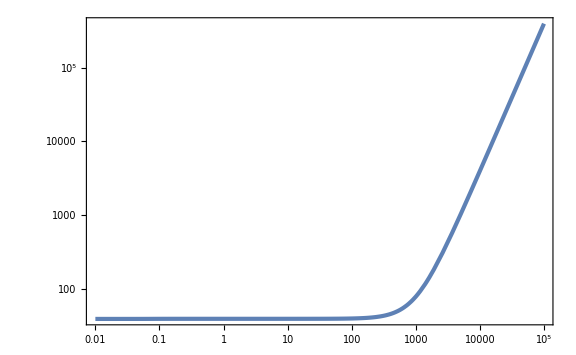

```mathematica
LogLogPlot[PζkL[-x],{x,10^-2,10^5}]
```

```mathematica
AbsoluteTiming[kS=10^1;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τ0->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
(*{fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τsm,τsp},WorkingPrecision->30,MaxRecursion->12],
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τem,τep},WorkingPrecision->30,MaxRecursion->12]}*)
fNL=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-10^-2},WorkingPrecision->30,MaxRecursion->15]]
```

NIntegrate::precw: The precision of the argument function (Im[((4.4024498666482342928580505328×10^6-1.06690167037495808438403477×10^6 ⅈ) «4» η'[τp])/(τp^2 Conjugate[z[τp]]^2)]) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in τp near {τp} = {-0.084383730135628347911387033035496318634186101798413489616637060453306482191557232}. NIntegrate obtained 0.13116257512096395655445244831849766049843459801555876042533018437182006582077601 and 0.18608694436090565671520712800295296847865341796677568163246491892300171722154899 for the integral and error estimates.

{6.33589,4.872207484526397364746180222}

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τ0->τiS,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ];
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
(*fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τsm,τsp}(*,WorkingPrecision->30*)]//Quiet;
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,τem,τep}(*,WorkingPrecision->30*)]//Quiet;*)
fNL=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[(ϵ[τp]η'[τp])/(τp^2 H^2)pktk[-10^-2,τp]/.{H->Hs}],{τp,-3,-10^-2},WorkingPrecision->30,MaxRecursion->15]//Quiet;
{kS,calPζkS[-10^-2],(*fNLs,fNLe*)fNL},{lnk,-3,2,10^-2}];//AbsoluteTiming
```

{509.98,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];(*
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];*)
fNLList=Map[{#[[1]],#[[3]](*+#[[4]]*)}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

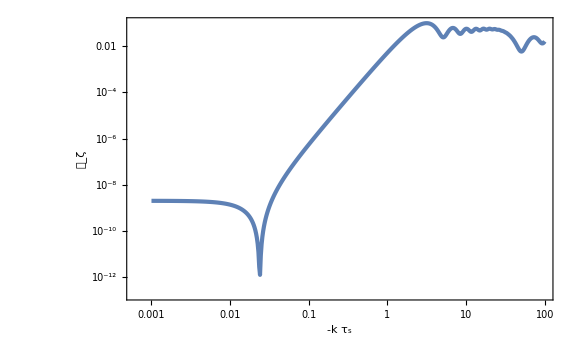

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

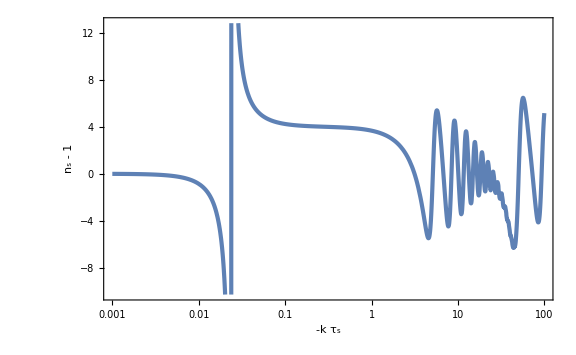

```mathematica
LogLinearPlot[nsm1[k],{k,10^-3,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

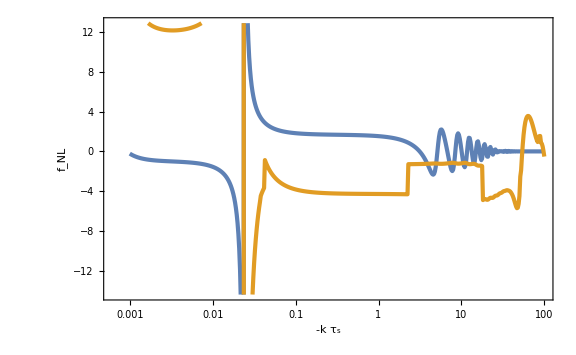

```mathematica
(*ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]*)
```

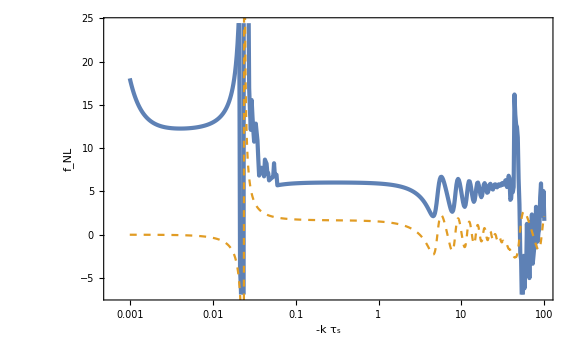

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[5/12 nsm1[k],{k,10^-3,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

### kL = 10

```mathematica
kL=10;
τiL=-10^2/kL;
vkL[τ_]=vk[τ]/.NDSolve[{EoM,vk[τi]==1/Sqrt[2k],vk'[τi]==-I Sqrt[k/2]}/.{τs->-1,τi->τiL,lnDt->lndt,k->kL},vk[τ],{τ,τiL,-10^-2},WorkingPrecision->30][[1]];
```

```mathematica
ζkL[τ_]=vkL[τ]/z[τ]/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2};
PζkL[τ_]=Norm[ζkL[τ]]^2;
```

```mathematica
calPkfNLList=ParallelTable[kS=10^lnk;
τiS=Min[-10^2/kS,-3];
vkS[τ_]=vk[τ]/.NDSolve[{EoM,vk[τ0]==1/Sqrt[2k],vk'[τ0]==-I Sqrt[k/2]}/.{τs->-1,τ0->τiS,lnDt->lndt,k->kS},vk[τ],{τ,τiS,-10^-2},WorkingPrecision->30,MaxSteps->10^5][[1]];
ζkS[τ_]=vkS[τ]/z[τ]/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2};
PζkS[τ_]=Norm[ζkS[τ]]^2;
calPζkS[τ_]=kS^3/(2 π^2)PζkS[τ];
pktk[τ_,τp_]=ζkL[τ]ζkS[τ]ζkS[τ]Conjugate[ζkL[τp]]Conjugate[ζkS[τp]]Conjugate[ζkS'[τp]];
fNLs=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[((ϵ[τp]η'[τp])/(τp^2 H^2)/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2,H->Hs})pktk[-10^-2,τp]],{τp,-3,(*-10^-2*)-1/3},WorkingPrecision->30]//Quiet;
fNLe=5/3 1/(PζkL[-10^-2]PζkS[-10^-2])NIntegrate[Im[((ϵ[τp]η'[τp])/(τp^2 H^2)/.{τs->-1,τ0->-10^5,lnDt->lndt,ϵ0->10^-2,H->Hs})pktk[-10^-2,τp]],{τp,-3 10^-lndt,-10^-2},WorkingPrecision->30]//Quiet;
{kS,calPζkS[-10^-2],fNLs,fNLe},{lnk,1,2,10^-2}];//AbsoluteTiming
```

{44.9342,Null}

```mathematica
calPkList=Map[{#[[1]],#[[2]]}&,calPkfNLList];
fNLsList=Map[{#[[1]],#[[3]]}&,calPkfNLList];
fNLeList=Map[{#[[1]],#[[4]]}&,calPkfNLList];
fNLList=Map[{#[[1]],#[[3]]+#[[4]]}&,calPkfNLList];
calPkint[k_]=Interpolation[calPkList][k];
nsm1[k_]=k D[Log[calPkint[k]], k];
```

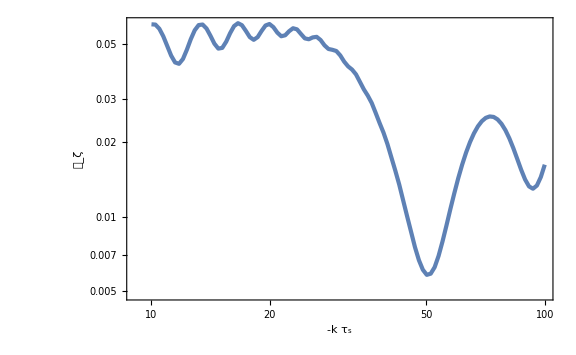

```mathematica
ListLogLogPlot[calPkList,FrameLabel->{-k Subscript[τ, s],Subscript[𝒫, ζ]}]
```

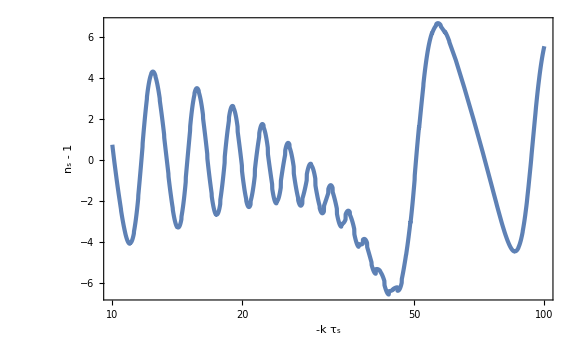

```mathematica
LogLinearPlot[nsm1[k],{k,10,10^2},FrameLabel->{-k Subscript[τ, s],"n_s - 1"}]
```

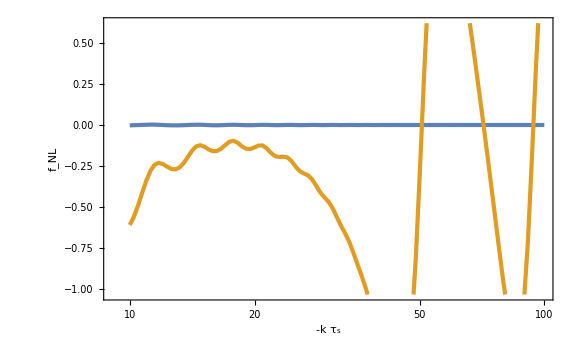

```mathematica
ListLogLinearPlot[{fNLsList,fNLeList},FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}]
```

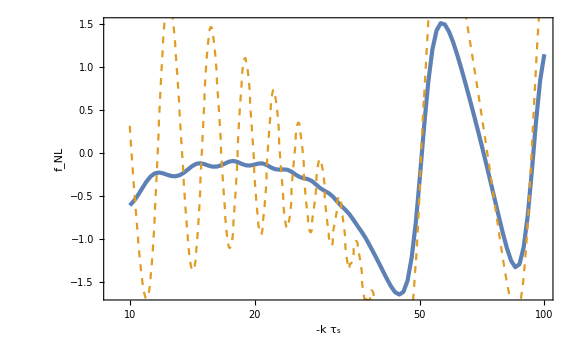

```mathematica
Show[ListLogLinearPlot[fNLList,FrameLabel->{-k Subscript[τ, s],Subscript[f, NL]}],LogLinearPlot[5/12 nsm1[k],{k,10,10^2},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```